## Control effort differs greatly in different directions (Prob. 14.12)

```mathematica
Clear["Global`*"];
```

Example adapted from Yan et al., Nat. Physics 2015  
(switched input from x1 to x2, to have more vertical image).

```mathematica
a=({{-3.2, 1.3, 1}, {1.3, -2.7, 0.7}, {1, 0.7, -2.2}});b=({{0}, {1}, {0}});sys=StateSpaceModel[{a,b}];
Wc=ControllabilityMatrix[sys]; {MatrixForm[Wc],MatrixRank[Wc],Det[Wc]}
```

{(0 | 1.3 | -6.97
1 | -2.7 | 9.47
0 | 0.7 | -2.13),3,-2.11}

```mathematica
{ev=Eigenvalues[a],First@#/Last@#&@ ev   (* condition number of a *) }
```

{{-4.33876,-3.07051,-0.690725},6.28145}

```mathematica
Wg=ControllabilityGramian[sys];{MatrixForm[Wg],MatrixRank[Wg],Det[Wg]}
```

{(0.045825 | 0.0798624 | 0.042819
0.0798624 | 0.241266 | 0.0679964
0.042819 | 0.0679964 | 0.0410984),3,3.07845×10^-6}

```mathematica
{ev=Eigenvalues[Wg],First@#/Last@#&@ev}
```

{{0.294162,0.033717,0.000310382},947.743}

```mathematica
Wgram[τ_]:=Integrate[MatrixExp[a t].b.bᵀ.MatrixExp[aᵀt],{t,0,τ}];Wgram[3]//MatrixForm
```

(0.0447457 | 0.0787321 | 0.0415803
0.0787321 | 0.240082 | 0.0666993
0.0415803 | 0.0666993 | 0.039677)

```mathematica
{ev=Eigenvalues[Wgram[3]],First@#/Last@#&@ev  (* almost same as τ -> ∞ case *)}
```

{{0.291359,0.0328491,0.000297533},979.249}

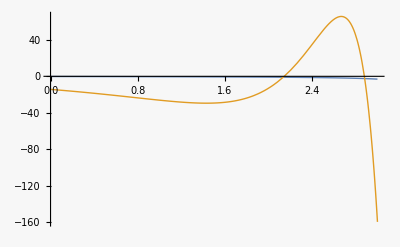

```mathematica
evec=Eigenvectors[Wgram[3]];uopt=bᵀ.MatrixExp[aᵀ(τ-t)].Inverse[Wgram[τ]].n;
uoptMAX=uopt/.{τ->3,n-> evec[[1]]};
uoptMIN=uopt/.{τ->3,n-> evec[[3]]};
Plot[{uoptMAX,uoptMIN},{t,0.,3.},PlotRange->All]
```

```mathematica
effort[n_]:=n.Inverse[Wgram[3]].n
```

```mathematica
evec=Eigenvectors[Wgram[3]];{emax=effort[evec[[3]]],emin=effort[evec[[1]]],emax/emin}
```

{3360.98,3.4322,979.249}

```mathematica
evec
```

{{-0.335246,-0.895506,-0.292708},{0.600442,-0.442501,0.66608},{0.726002,-0.0475463,-0.686047}}

Try a simpler 2d version.  [Use this one for the book!]

```mathematica
a1=({{-3.2, 1.3}, {1.3, -2.7}}); b1=({{0}, {1}}); sys1=StateSpaceModel[{a1,b1}];Wc1=ControllabilityMatrix[sys1];{MatrixForm[Wc1],MatrixRank[Wc1],Det[Wc1]}
```

{(0 | 1.3
1 | -2.7),2,-1.3}

```mathematica
Wg1=ControllabilityGramian[sys1]; {MatrixForm[Wg1],MatrixRank[Wg1],Det[Wg1]}
```

{(0.0206072 | 0.0507255
0.0507255 | 0.209609),2,0.00174638}

```mathematica
{ev=Eigenvalues[a1],First@#/Last@#&@ev}
```

{{-4.27382,-1.62618},2.62814}

```mathematica
{ev=Eigenvalues[Wg1],First@#/Last@#&@ev}
```

{{0.222362,0.00785375},28.3128}

```mathematica
Wgram1[τ_]:=Integrate[MatrixExp[a1 t].b1.b1ᵀ.MatrixExp[a1ᵀt],{t,0,τ}];Wgram1[3]//MatrixForm
```

(0.020603 | 0.0507203
0.0507203 | 0.209602)

```mathematica
{ev=Eigenvalues[Wgram1[3]],First@#/Last@#&@ev}
```

{{0.222353,0.0078518},28.3188}

```mathematica
effort1[n_]:=n.Inverse[Wgram1[3]].n;evec1=Eigenvectors[Wgram1[3]];effort1[evec1[[2]]]/effort1[evec1[[1]]]
```

28.3188

```mathematica
{evec1[[2]]//MatrixForm,evec1[[1]]//MatrixForm}
```

{(-0.969822
0.243814),(0.243814
0.969822)}

```mathematica
ArcTan[evec1[[2]][[1]],evec1[[2]][[2]]]-π
```

-0.246297

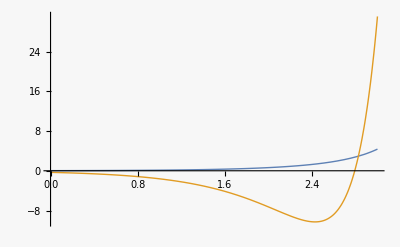

```mathematica
uopt1=b1ᵀ.MatrixExp[a1ᵀ(τ-t)].Inverse[Wgram1[τ]].n;
uoptMAX1=(uopt1/.{τ->3,n-> evec1[[1]]})[[1]];
uoptMIN1=(uopt1/.{τ->3,n-> evec1[[2]]})[[1]];
Plot[{uoptMAX1,uoptMIN1},{t,0.,3.},PlotRange->All]
```

```mathematica
udat=Table[{uoptMAX1,uoptMIN1},{t,0,3,0.01}];
(* Export["controlEffort2.dat",udat] *)
```

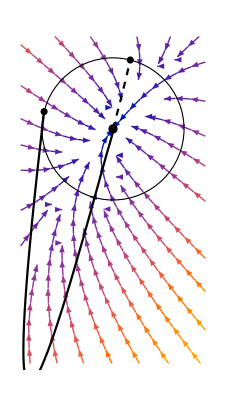

```mathematica
splot=StreamPlot[a1.({{x}, {y}}),{x,-1.3,1.3},{y,-3.3,1.3}, StreamPoints->Coarse,AspectRatio->Automatic,StreamStyle->GrayLevel[0.85],(* Background->GrayLevel[0.95], *)  Frame->None];
circ=Graphics[{Thickness[0.002],Black,Circle[]}];marker0=Graphics[{Thin,Disk[{0,0},0.065]}];
marker1=Graphics[{Thin,Disk[Eigenvectors[Wgram1[3]][[1]],0.05]}];
marker2=Graphics[{Thin,Disk[Eigenvectors[Wgram1[3]][[2]],0.05]}];

out1a=OutputResponse[sys1,uoptMAX1,{t,0,3}];
p1a=ParametricPlot[{out1a[[1]],out1a[[2]]},{t,0,3},PlotStyle->{Black,Dashed}];
out1b=OutputResponse[sys1,uoptMIN1,{t,0,3}];
p1b=ParametricPlot[{out1b[[1]],out1b[[2]]},{t,0,3},PlotStyle->Black];

allplots=Show[splot,circ,marker0,marker1,marker2,p1b,p1a]
```

The control efforts for the BEST directions are roughly the same, as we go from n=2 to n=3.

```mathematica
{effort1[evec1[[1]]],effort[evec[[1]]]}
```

{4.49734,3.4322}

The control efforts for the WORST directions are very different.

```mathematica
{effort1[evec1[[2]]],effort[evec[[3]]]}
```

{127.359,3360.98}